# Natario zero expansion drive

## Shift field

```mathematica
ClearAll[vx,vy, vz,r];
r=Sqrt[(x-u*t)^2+y^2+z^2];

vx=(u/2)(2f[r]+(y^2+z^2)/r*f'[r]);
vy=-(u/2)*((x-u*t)*y)/r*f'[r];
vz=-(u/2)*((x-u*t)*z)/r*f'[r];

FullSimplify[D[vx,x]+D[vy,y]+D[vz,z]]

ClearAll[vx,vy, vz,r];
```

0

## Code strings

### Proper formatting of Power

```mathematica
Unprotect[Power];
Format[Power[E,a_],CForm]:=(exp[a]);
Format[Power[a_,1/2],CForm]:=(sqrt[a]);
Format[Power[a_,-1/2],CForm]:=(1/sqrt[a]);
Format[Power[a_,3/2],CForm]:=(HoldForm[sqrt[a]^3]);
Format[Power[a_,b_],CForm]:=(powi[a,b])/;b∈Integers;
Format[Power[a_,b_],CForm]:=(powf[a,b]);
Protect[Power];
```

### Transition functions

```mathematica
ClearAll[deg,poly];
deg=9;
poly[x_]=Sum[c[i]x^i,{i,0,deg}];

ClearAll[polyCs];
polyCs=Solve[
{
poly[x0]==y0,
poly[x0+dx]==0,
Derivative[1][poly][x0]==0,
Derivative[1][poly][x0+dx]==0,

Derivative[2][poly][x0]==0,
Derivative[2][poly][x0+dx]==0,

Derivative[3][poly][x0]==0,
Derivative[3][poly][x0+dx]==0,

Derivative[4][poly][x0]==0,
Derivative[4][poly][x0+dx]==0
},
Table[c[i],{i,0,deg}]
]//Flatten//FullSimplify;

ClearAll[polyWithCs];
polyWithCs=FullSimplify[poly[x]//.polyCs]

ClearAll[polyTrans];
polyTrans[x_,y0_,x0_,dx_]:=Piecewise[
{
{y0,x<x0},
{0,x>(x0+dx)},
{((dx^4+5 dx^3 (x-x0)+15 dx^2 (x-x0)^2+35 dx (x-x0)^3+70 (x-x0)^4) (dx-x+x0)^5 y0)/dx^9,True}
}
]
```

((dx^4+5 dx^3 (x-x0)+15 dx^2 (x-x0)^2+35 dx (x-x0)^3+70 (x-x0)^4) (dx-x+x0)^5 y0)/dx^9

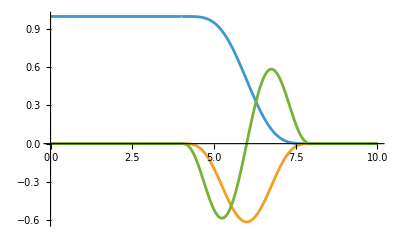

```mathematica
Plot[
{
Derivative[0,0,0,0][polyTrans][x,1,4,4],
Derivative[1,0,0,0][polyTrans][x,1,4,4],
Derivative[2,0,0,0][polyTrans][x,1,4,4]
},
{x,0,10}
]
```

```mathematica
FullSimplify[polyTrans[r,1,radius,sigma]]
```

Piecewise[{{1, r<radius}, {0, r>radius+sigma}, {((-r+radius+sigma)^5 (70 (r-radius)^4+35 (r-radius)^3 sigma+15 (r-radius)^2 sigma^2+5 (r-radius) sigma^3+sigma^4))/sigma^9, True}}]

```mathematica
ClearAll[strRules];
strRules={
"powi"->"f64::powi",
"sigma"->"self.sigma",
"radius"->"self.radius"
};

ClearAll[transCore];
transCore=((-r+radius+sigma)^4 (20 (r-radius)^3+10 (r-radius)^2 sigma+4 (r-radius) sigma^2+sigma^3))/sigma^7;

Print[
"fn trans(&self, r: f64) -> f64 {",
"if r < self.radius {1.0} else if r > (self.radius + self.sigma) {0.0} else {",
StringReplace[ToString[transCore//N,CForm],strRules],
"}}\n"
]

Print[
"fn d_trans_dr(&self, r: f64) -> f64 {",
"if r < self.radius || r > (self.radius + self.sigma) {0.0} else {",
StringReplace[ToString[D[transCore,r]//N,CForm],strRules],
"}}\n"
]

Print[
"fn d2_trans_dr2(&self, r: f64) -> f64 {",
"if r < self.radius || r > (self.radius + self.sigma) {0.0} else {",
StringReplace[ToString[D[transCore,{r,2}]//N,CForm],strRules],
"}}\n"
]

ClearAll[strRules];
ClearAll[transCore];
```

fn trans(&self, r: f64) -> f64 {if r < self.radius {1.0} else if r > (self.radius + self.sigma) {0.0} else {(f64::powi(-1.*r + self.radius + self.sigma,4)*(20.*f64::powi(r - 1.*self.radius,3) + 10.*f64::powi(r - 1.*self.radius,2)*self.sigma + 4.*(r - 1.*self.radius)*f64::powi(self.sigma,2) + f64::powi(self.sigma,3)))/f64::powi(self.sigma,7)}}

fn d_trans_dr(&self, r: f64) -> f64 {if r < self.radius || r > (self.radius + self.sigma) {0.0} else {(f64::powi(-1.*r + self.radius + self.sigma,4)*(60.*f64::powi(r - 1.*self.radius,2) + 20.*(r - 1.*self.radius)*self.sigma + 4.*f64::powi(self.sigma,2)))/f64::powi(self.sigma,7) - (4.*f64::powi(-1.*r + self.radius + self.sigma,3)*(20.*f64::powi(r - 1.*self.radius,3) + 10.*f64::powi(r - 1.*self.radius,2)*self.sigma + 4.*(r - 1.*self.radius)*f64::powi(self.sigma,2) + f64::powi(self.sigma,3)))/f64::powi(self.sigma,7)}}

fn d2_trans_dr2(&self, r: f64) -> f64 {if r < self.radius || r > (self.radius + self.sigma) {0.0} else {(f64::powi(-1.*r + self.radius + self.sigma,4)*(120.*(r - 1.*self.radius) + 20.*self.sigma))/f64::powi(self.sigma,7) - (8.*f64::powi(-1.*r + self.radius + self.sigma,3)*(60.*f64::powi(r - 1.*self.radius,2) + 20.*(r - 1.*self.radius)*self.sigma + 4.*f64::powi(self.sigma,2)))/f64::powi(self.sigma,7) + (12.*f64::powi(-1.*r + self.radius + self.sigma,2)*(20.*f64::powi(r - 1.*self.radius,3) + 10.*f64::powi(r - 1.*self.radius,2)*self.sigma + 4.*(r - 1.*self.radius)*f64::powi(self.sigma,2) + f64::powi(self.sigma,3)))/f64::powi(self.sigma,7)}}

### Radius functions and derivatives

```mathematica
ClearAll[strRules];
strRules={
"u"->"self.u",
"sqrt"->"f64::sqrt",
"epsilon"->"self.epsilon",
"pos"->"self.get_bubble_position",
"powi"->"f64::powi"
};

ClearAll[r];
r=Sqrt[(x-pos[t])^2+y^2+z^2+epsilon];

Print[
"fn r(&self, t: f64, x: f64, y: f64, z: f64) -> f64 {",
StringReplace[ToString[r,CForm],strRules],
"}\n"
]

Print[
"fn d_r_dx(&self, t: f64, x: f64, y: f64, z: f64) -> f64 {",
StringReplace[ToString[FullSimplify[D[r,x]],CForm],strRules],
"}\n"
]

Print[
"fn d_r_dy(&self, t: f64, x: f64, y: f64, z: f64) -> f64 {",
StringReplace[ToString[FullSimplify[D[r,y]],CForm],strRules],
"}\n"
]

Print[
"fn d_r_dz(&self, t: f64, x: f64, y: f64, z: f64) -> f64 {",
StringReplace[ToString[FullSimplify[D[r,z]],CForm],strRules],
"}\n"
]

ClearAll[r];
ClearAll[strRules];
```

fn r(&self, t: f64, x: f64, y: f64, z: f64) -> f64 {f64::sqrt(self.epsilon + f64::powi(y,2) + f64::powi(z,2) + f64::powi(x - self.get_bubble_position(t),2))}

fn d_r_dx(&self, t: f64, x: f64, y: f64, z: f64) -> f64 {(x - self.get_bubble_position(t))/f64::sqrt(self.epsilon + f64::powi(y,2) + f64::powi(z,2) + f64::powi(x - self.get_bubble_position(t),2))}

fn d_r_dy(&self, t: f64, x: f64, y: f64, z: f64) -> f64 {y/f64::sqrt(self.epsilon + f64::powi(y,2) + f64::powi(z,2) + f64::powi(x - self.get_bubble_position(t),2))}

fn d_r_dz(&self, t: f64, x: f64, y: f64, z: f64) -> f64 {z/f64::sqrt(self.epsilon + f64::powi(y,2) + f64::powi(z,2) + f64::powi(x - self.get_bubble_position(t),2))}

### Derivatives of vx, vy and vz

```mathematica
ClearAll[strRules];
strRules={
"radius"->"self.radius",
"sigma"->"self.sigma",
"u"->"self.u",
"powi"->"f64::powi",
"pos"->"self.get_bubble_position"
};

ClearAll[rulesA,rulesB];
rulesA={
r[t,x,y,z]->lr,

D[r[t,x,y,z],x]->drdx,
D[r[t,x,y,z],y]->drdy,
D[r[t,x,y,z],z]->drdz,

D[r[t,x,y,z],{x,2}]->d2rdx2,
D[r[t,x,y,z],{y,2}]->d2rdy2,
D[r[t,x,y,z],{z,2}]->d2rdz2
};

rulesB={
f[lr]->lf,
Derivative[1][f][lr]->dfdr,
Derivative[2][f][lr]->d2fdr2
};

ClearAll[vx,vy,vz];
vx=(u/2)(2f[r[t,x,y,z]]+(y^2+z^2)/r[t,x,y,z]*f'[r[t,x,y,z]]);
vy=-(u/2)*((x-pos[t])*y)/r[t,x,y,z]*f'[r[t,x,y,z]];
vz=-(u/2)*((x-pos[t])*z)/r[t,x,y,z]*f'[r[t,x,y,z]];

Print[
"fn vx(&self, q: &nalgebra::Vector4<f64>) -> f64 {",
StringReplace[ToString[vx//.rulesA//.rulesB,CForm],strRules],"}\n"
]

Print[
"fn vy(&self, q: &nalgebra::Vector4<f64>) -> f64 {",
StringReplace[ToString[vy//.rulesA//.rulesB,CForm],strRules],"}\n"
]

Print[
"fn vz(&self, q: &nalgebra::Vector4<f64>) -> f64 {",
StringReplace[ToString[vz//.rulesA//.rulesB,CForm],strRules],"}\n"
]

Print[
"fn d_vx_dx(&self, q: &nalgebra::Vector4<f64>) -> f64 {",
StringReplace[ToString[D[vx,x]//.rulesA//.rulesB,CForm],strRules],"}\n"
]

Print[
"fn d_vx_dy(&self, q: &nalgebra::Vector4<f64>) -> f64 {",
StringReplace[ToString[D[vx,y]//.rulesA//.rulesB,CForm],strRules],"}\n"
]

Print[
"fn d_vx_dz(&self, q: &nalgebra::Vector4<f64>) -> f64 {",
StringReplace[ToString[D[vx,z]//.rulesA//.rulesB,CForm],strRules],"}\n"
]

Print[
"fn d_vy_dx(&self, q: &nalgebra::Vector4<f64>) -> f64 {",
StringReplace[ToString[D[vy,x]//.rulesA//.rulesB,CForm],strRules],"}\n"
]

Print[
"fn d_vy_dy(&self, q: &nalgebra::Vector4<f64>) -> f64 {",
StringReplace[ToString[D[vy,y]//.rulesA//.rulesB,CForm],strRules],"}\n"
]

Print[
"fn d_vy_dz(&self, q: &nalgebra::Vector4<f64>) -> f64 {",
StringReplace[ToString[D[vy,z]//.rulesA//.rulesB,CForm],strRules],"}\n"
]

Print[
"fn d_vz_dx(&self, q: &nalgebra::Vector4<f64>) -> f64 {",
StringReplace[ToString[D[vz,x]//.rulesA//.rulesB,CForm],strRules],"}\n"
]

Print[
"fn d_vz_dy(&self, q: &nalgebra::Vector4<f64>) -> f64 {",
StringReplace[ToString[D[vz,y]//.rulesA//.rulesB,CForm],strRules],"}\n"
]

Print[
"fn d_vz_dz(&self, q: &nalgebra::Vector4<f64>) -> f64 {",
StringReplace[ToString[D[vz,z]//.rulesA//.rulesB,CForm],strRules],"}\n"
]

ClearAll[strRules];
ClearAll[rulesA,rulesB];
ClearAll[vx,vy,vz];
```

fn vx(&self, q: &nalgebra::Vector4<f64>) -> f64 {(self.u*(2*lf + (dfdr*(f64::powi(y,2) + f64::powi(z,2)))/lr))/2.}

fn vy(&self, q: &nalgebra::Vector4<f64>) -> f64 {-0.5*(dfdr*self.u*y*(x - self.get_bubble_position(t)))/lr}

fn vz(&self, q: &nalgebra::Vector4<f64>) -> f64 {-0.5*(dfdr*self.u*z*(x - self.get_bubble_position(t)))/lr}

fn d_vx_dx(&self, q: &nalgebra::Vector4<f64>) -> f64 {(self.u*(2*dfdr*drdx - (dfdr*drdx*(f64::powi(y,2) + f64::powi(z,2)))/f64::powi(lr,2) + (d2fdr2*drdx*(f64::powi(y,2) + f64::powi(z,2)))/lr))/2.}

fn d_vx_dy(&self, q: &nalgebra::Vector4<f64>) -> f64 {(self.u*(2*dfdr*drdy + (2*dfdr*y)/lr - (dfdr*drdy*(f64::powi(y,2) + f64::powi(z,2)))/f64::powi(lr,2) + (d2fdr2*drdy*(f64::powi(y,2) + f64::powi(z,2)))/lr))/2.}

fn d_vx_dz(&self, q: &nalgebra::Vector4<f64>) -> f64 {(self.u*(2*dfdr*drdz + (2*dfdr*z)/lr - (dfdr*drdz*(f64::powi(y,2) + f64::powi(z,2)))/f64::powi(lr,2) + (d2fdr2*drdz*(f64::powi(y,2) + f64::powi(z,2)))/lr))/2.}

fn d_vy_dx(&self, q: &nalgebra::Vector4<f64>) -> f64 {-0.5*(dfdr*self.u*y)/lr + (dfdr*drdx*self.u*y*(x - self.get_bubble_position(t)))/(2.*f64::powi(lr,2)) - (d2fdr2*drdx*self.u*y*(x - self.get_bubble_position(t)))/(2.*lr)}

fn d_vy_dy(&self, q: &nalgebra::Vector4<f64>) -> f64 {-0.5*(dfdr*self.u*(x - self.get_bubble_position(t)))/lr + (dfdr*drdy*self.u*y*(x - self.get_bubble_position(t)))/(2.*f64::powi(lr,2)) - (d2fdr2*drdy*self.u*y*(x - self.get_bubble_position(t)))/(2.*lr)}

fn d_vy_dz(&self, q: &nalgebra::Vector4<f64>) -> f64 {(dfdr*drdz*self.u*y*(x - self.get_bubble_position(t)))/(2.*f64::powi(lr,2)) - (d2fdr2*drdz*self.u*y*(x - self.get_bubble_position(t)))/(2.*lr)}

fn d_vz_dx(&self, q: &nalgebra::Vector4<f64>) -> f64 {-0.5*(dfdr*self.u*z)/lr + (dfdr*drdx*self.u*z*(x - self.get_bubble_position(t)))/(2.*f64::powi(lr,2)) - (d2fdr2*drdx*self.u*z*(x - self.get_bubble_position(t)))/(2.*lr)}

fn d_vz_dy(&self, q: &nalgebra::Vector4<f64>) -> f64 {(dfdr*drdy*self.u*z*(x - self.get_bubble_position(t)))/(2.*f64::powi(lr,2)) - (d2fdr2*drdy*self.u*z*(x - self.get_bubble_position(t)))/(2.*lr)}

fn d_vz_dz(&self, q: &nalgebra::Vector4<f64>) -> f64 {-0.5*(dfdr*self.u*(x - self.get_bubble_position(t)))/lr + (dfdr*drdz*self.u*z*(x - self.get_bubble_position(t)))/(2.*f64::powi(lr,2)) - (d2fdr2*drdz*self.u*z*(x - self.get_bubble_position(t)))/(2.*lr)}